## MPC Hawk/dove Scale

import images
extract  faces
import labels
make chart

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"img"}]
```

Z:\Dubai\Research\Bloomberg Economics\RussiaCEE\data\RUS\xdata\bankofrussia\mpc\img

```mathematica
photo=Import[#]&/@FileNames[All,dir];
```

```mathematica
faceextract[img_]:=Module[{
face=First@FindFaces[img,"Image",PaddingSize->600]
,disk=Graphics[Disk[],Background->White]
,diskim
}
,diskim=ColorConvert[Rasterize[disk,ImageSize->ImageDimensions[face]],"Grayscale"];
Rasterize[ColorCombine[{face,ColorNegate@diskim},"RGB"],RasterSize->200,Background->None]

]
```

```mathematica
faces=faceextract/@photo;
```

```mathematica
dir="Z:\\Dubai\\Research\\Bloomberg Economics\\RussiaCEE\\data\\RUS\\xdata\\bankofrussia\\mpc"
```

Z:\Dubai\Research\Bloomberg Economics\RussiaCEE\data\RUS\xdata\bankofrussia\mpc

```mathematica
hawk=-Graphics-;
dove=-Graphics-;
```

Positions are random --- to use real scores you’ll need some changes

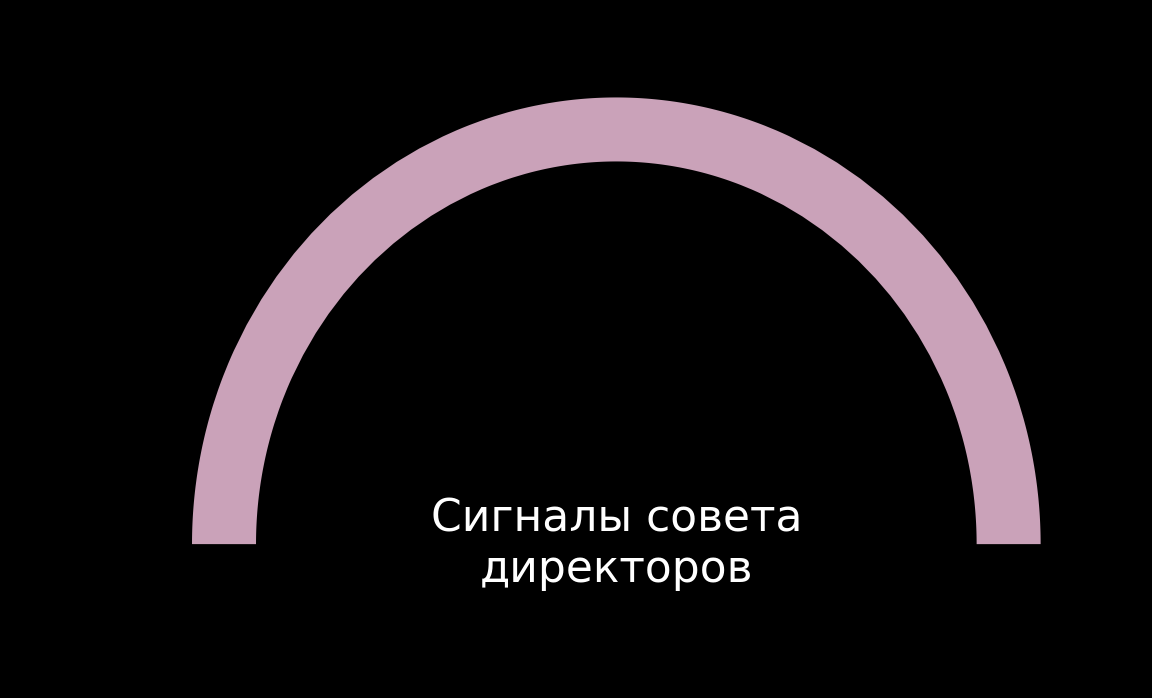
Key rate survey: expected vs. decisions
-Graphics-
Source: Bloomberg, VTB Capital Research.

```mathematica
ParametricPlot[{Cos[u], Sin[u]}
,{u,0, Pi}
,PlotStyle->Thickness[0.04]
,ColorFunction->Function[{x,y,u,v},Blend[{$ThemeColorDataIndexed@2,White,Red},x]]
,Epilog->{

Sequence@@MapIndexed[
Inset[
#1,
{1.1Cos[Rescale[First@#2,{1,13},{0,Pi}]],1.1 Sin[Rescale[First@#2,{1,13},{0,Pi}]]}
,Automatic
,0.2
]&,
RandomSample@faces]
,White
,Text[ThemeTextStyle["Сигналы совета\nдиректоров",FontSize->2$ThemeFontSizeLarge]]

}
,PlotRange->{{-1.2,1.2},{-0.2,1.2}}
,FrameTicks->{{None,None},{{{-1,hawk},{1,dove}},None}}
,Axes->False
,Frame->{{False,False},{True,False}}
]
```